ⅇ^(-Abs[x]) x^2

25

0.135179

3

-1

{{-2,0.516948},{-46/25,0.513464},{-42/25,0.50232},{-38/25,0.482543},{-34/25,0.453329},{-6/5,0.414176},{-26/25,0.36507},{-22/25,0.306734},{-18/25,0.240962},{-14/25,0.17106},{-2/5,0.102418},{-6/25,0.0432681},{-2/25,0.00564173},{2/25,0.00564173},{6/25,0.0432681},{2/5,0.102418},{14/25,0.17106},{18/25,0.240962},{22/25,0.306734},{26/25,0.36507},{6/5,0.414176},{34/25,0.453329},{38/25,0.482543},{42/25,0.50232},{46/25,0.513464},{2,0.516948}}

0.0230253-2.17733×10^-16 x+0.469419 x^2+1.35656×10^-16 x^3-0.157785 x^4-8.04002×10^-17 x^5+0.0179526 x^6+1.60773×10^-17 x^7

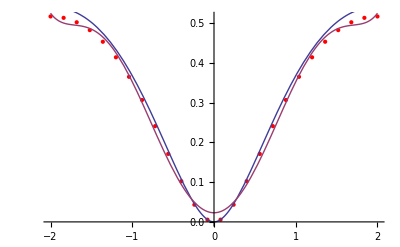

```mathematica
F[x_] = Exp[-Abs[x]]*x^2
m = 25
z = RandomReal[{0,1}]
c = RandomInteger [{1, 5}]
If[z<0.5, k = -1, k=1]

data = Table[{x, F[x]*(1+k*z/c)},{x, -2, 2, 4/m}]
G[x_] = Fit[data,{1,x,x^2, x^3,x^4,x^5,x^6,x^7},x]
Show[ListPlot[data,PlotStyle->Red],Plot[{F[x],G[x]},{x,-2,2}]]
```